## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
<<IGraphM`
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"BigSur 8.nb"}]];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"Additional Bioinformatics Functions.nb"}]];
```

IGraph/M 0.6.2 (July 25, 2022)
Evaluate IGDocumentation[] to get started.

ReplacePart::argrx: ReplacePart called with 2 arguments; 3 arguments are expected.

```mathematica
lowcRows[l_,min_]:=With[{x=Transpose[l]},Select[Range[Length[x]],Total[x[[#]]]>=min&]];
lowExRows[mat_, x_]:= Module[{means},
means = Mean/@mat;
Select[Range[Length[means]],means[[#]]>=x&]
];
```

## Load data

```mathematica
smallTest = Import["../testthat/fixtures/test_counts.mtx"];
```

```mathematica
smallTestGenes = Import["../testthat/fixtures/test_Genes.csv"][[2;;]];
```

```mathematica
smallTestCells = Import["../testthat/fixtures/test_Cells.csv"][[2;;]];
```

```mathematica
Dimensions[smallTest]
```

{254,250}

```mathematica
smallTestMatpac = {smallTest, smallTestGenes, smallTestCells};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica

```mathematica
rajFull = Import["../testthat/fixtures/arjunrajrawcounts2.mtx"];
rajGenes = Import["../testthat/fixtures/arjunrajgenenames2.csv"];
rajCells = Import["../testthat/fixtures/arjunrajcellnames2.csv"];
```

```mathematica
kcells= lowcRows[rajFull,1300];
```

```mathematica
Length[kcells]
```

3117

```mathematica
kgenes = lowExRows[rajFull, 0.001];
```

```mathematica
Length[kgenes]
```

14695

```mathematica
Min[Total/@rajFull]
```

8

```mathematica
rajMatpac = {rajFull[[kgenes,kcells]], Flatten[rajGenes][[kgenes]], Flatten[rajCells][[kcells]]};
```

```mathematica
Dimensions/@rajMatpac
```

{{14695,3117},{14695},{3117}}

```mathematica
Export["../testthat/fixtures/rajSubs.mtx",rajMatpac[[1]]];
Export["../testthat/fixtures/rajSubGenes.csv",rajMatpac[[2]]];
Export["../testthat/fixtures/rajSubCells.csv", rajMatpac[[3]]];
```

## Residuals, eta/theta, and c’s

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

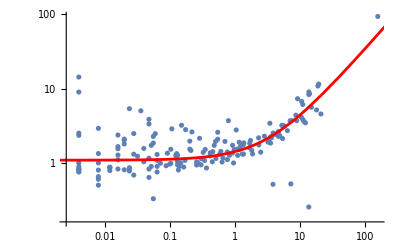

```mathematica
etaTheta=Values@TwoComponentCL1[smallTestMatpac, 250];
```

```mathematica
Export["etaTheta.txt", etaTheta]
```

etaTheta.txt

```mathematica
TwoComponentCL1All[matpac_]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data, params,params2},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
newmat=mat;
newgenetotals=genetotals;
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues=j/.FindRoot[#==-1+n, {j,1}, Method-> "Secant"]&/@Total/@((newmat-newematrix)^2/(newematrix(1+j newematrix))); 
data=Select[Transpose[{newgenetotals/n, 1+fittedjvalues*newgenetotals/n}], Last[#]>0&];
params=FindFit[Log[data], {Log[1+ η + θ*E^x],{η>0, θ>0}},  {{η,0}, {θ,0.1}}, x, NormFunction->(Total@Abs[#]&)];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+ η + θ*μ)/.params, {μ, 10^-6, 10^6}, PlotStyle-> Red]]];
params]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

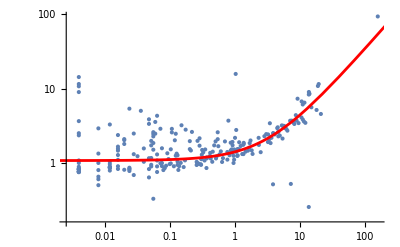

{0.0797936,0.331465}

```mathematica
etaTheta=Values@TwoComponentCL1All[smallTestMatpac]
```

```mathematica
Export["etaTheta.txt", etaTheta]
```

etaTheta.txt

```mathematica
TwoComponentCL1AllThetaOnly[matpac_]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data, params,params2},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
newmat=mat;
newgenetotals=genetotals;
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues=j/.FindRoot[#==-1+n, {j,1}, Method-> "Secant"]&/@Total/@((newmat-newematrix)^2/(newematrix(1+j newematrix))); 
data=Select[Transpose[{newgenetotals/n, 1+fittedjvalues*newgenetotals/n}], Last[#]>0&];
Print[Length[data]];
params=FindFit[Log[data], {Log[1+ θ*E^x],{ θ>0}},  {{θ,0.1}}, x, NormFunction->(Total@Abs[#]&)];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+ θ*μ)/.params, {μ, 10^-6, 10^6}, PlotStyle-> Red]]];
params]
```

```mathematica
Options[TwoComponentCThetaOnly]={"Sample Goal"-> 3000, "zero eta"->True };
TwoComponentCThetaOnly[matpac_, OptionsPattern[]]:=
Module[{mat,depthlist,n,genetotals, bl,genesample,newmat, newgenetotals, newematrix, fittedjvalues,data,stop,indices,θlist,temp, params, t1},
mat=matpac[[1]];
depthlist =(Total/@N[Transpose[mat]])/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
bl=BinLists[Log@genetotals->Range[Length[genetotals]], 0.5 ];
genesample=Flatten[RandomSample[#, Min[Length[#], Ceiling[OptionValue["Sample Goal"]/Length[bl]]]]&/@bl];
newmat=mat[[genesample]];
newgenetotals=genetotals[[genesample]];
indices=Partition[RandomSample[Range[Length[newgenetotals]]], UpTo[200]];
newematrix= KroneckerProduct[newgenetotals, depthlist];
fittedjvalues={};θlist={};data={};
For[k=1,k<= Length[indices],k++,
fittedjvalues=Join[fittedjvalues, Table[j/.FindRoot[Total@((newmat[[i]]/newematrix[[i]]-1)^2/(1/newematrix[[i]]+j )) +1-n, {j,1}, Method-> "Secant"], {i, indices[[k]]}]];
data=N[Select[Transpose[{newgenetotals[[Flatten[indices[[1;;k]]]]]/n, 1+fittedjvalues*newgenetotals[[Flatten[indices[[1;;k]]]]]/n}], Last[#]>0&]];
If[OptionValue["zero eta"],
params=Join[{η->0},FindFit[Log[data], {Log[1+ θ*E^x],θ>0},{{θ,0.1}}, x,NormFunction->{"HuberPenalty",0.01}]],
params=FindFit[Log[data], {Log[1+ η + θ*E^x],{η>0, θ>0}},  {{η,0}, {θ,0.1}}, x,NormFunction->{"HuberPenalty",0.01}]];
AppendTo[θlist,{k,θ/.params}];
NotebookDelete[t1];NotebookDelete[stop];
t1=PrintTemporary[Last/@θlist];
NotebookDelete[temp];
temp=PrintTemporary[Grid[{{
ListPlot[θlist, Joined-> True, PlotRange-> {{1,Length[indices]},{0,Automatic}}],
Show[ListLogLogPlot[data],LogLogPlot[(1+η+ θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red, Frame-> True, FrameLabel-> {"mean expression (μ)", "1+η+θμ"}]]
}}]];
stop=PrintTemporary[Button["Stop Operation",Print[Show[ListLogLogPlot[data],LogLogPlot[(1+η+ θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red, Frame-> True, FrameLabel-> {"mean expression (μ)", "1+η+θμ"}]]];
Print[{200k "genes tested", params}];FrontEndTokenExecute["EvaluatorAbort"]]];];
NotebookDelete[stop];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+η+ θ*μ)/.params, {μ, Min[First/@data], Max[First/@data]}, PlotRange-> All,  PlotStyle-> Red, Frame-> True, FrameLabel-> {"mean expression (μ)", "1+η+θμ"}]]];
{200k "genes tested", params}]
```

```mathematica
Options[TwoComponentCThetaOnlyVec]={"zero eta"->True,"Tolerance"->1.*^-12,"Max Iterations"->100};

TwoComponentCThetaOnlyVec[matpac_,OptionsPattern[]]:=Module[{mat,depthlist,n,genetotals,ematrix,a,b,lo,j,f,fp,jnew,bad,tol,maxit,k,data,params, keep, bin, counts, w},mat=matpac[[1]];
depthlist=Total/@N[Transpose[mat]]/Total[Flatten[mat]];
genetotals=Total/@mat;
n=Width[mat];
ematrix=KroneckerProduct[genetotals,depthlist];
a=(mat/ematrix-1)^2;
b=1/ematrix;
lo=-(Min/@b);(*j must exceed this per gene*)tol=OptionValue["Tolerance"];
maxit=OptionValue["Max Iterations"];
j=ConstantArray[1.,Length[genetotals]];
Do[f=(Total/@(a/(b+j)))-(n-1);
fp=-(Total/@(a/(b+j)^2));
jnew=j-f/fp;
bad=UnitStep[lo-jnew];(*1 where the step leaves the domain*)jnew=(1-bad) jnew+bad (j+lo)/2;(*bisect toward the pole instead*)If[Max[Abs[jnew-j]]<tol,j=jnew;Break[]];
j=jnew,{k,maxit}];
data=Transpose[{genetotals/n,1+j*genetotals/n}];keep=Flatten@Position[Last/@data,_?Positive];data=N[data[[keep]]];bin=Floor[Log[genetotals[[keep]]]/0.5];counts=Counts[bin];w=1./Sqrt[Lookup[counts,bin]];               (*each half-log bin contributes equally*)

params=Join[{η->0},FindFit[Log[data],{Log[1+θ*E^x],θ>0},{{θ,0.1}},x,NormFunction->(Total[w*Abs[#]]&), MaxIterations->1000]];
Print[Show[ListLogLogPlot[data],LogLogPlot[(1+η+θ*μ)/. params,{μ,Min[First/@data],Max[First/@data]},PlotRange->All,PlotStyle->Red,Frame->True,FrameLabel->{"mean expression (μ)","1+η+θμ"}]]];
{Length[genetotals] "genes tested",params}]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

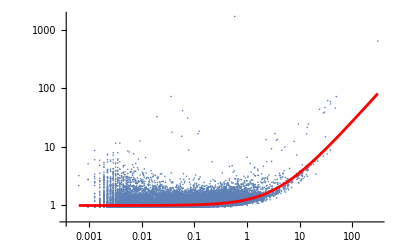

{14695 genes tested,{η→0,θ→0.261967}}

```mathematica
rajthetaOnly2=TwoComponentCThetaOnlyVec[rajMatpac]
```

{0.218825,0.244151,0.244703,0.245965,0.248588,0.250435,0.253968,0.251735,0.249854,0.25015,0.250144,0.248045,0.247823,0.248753,0.248495,0.248263}

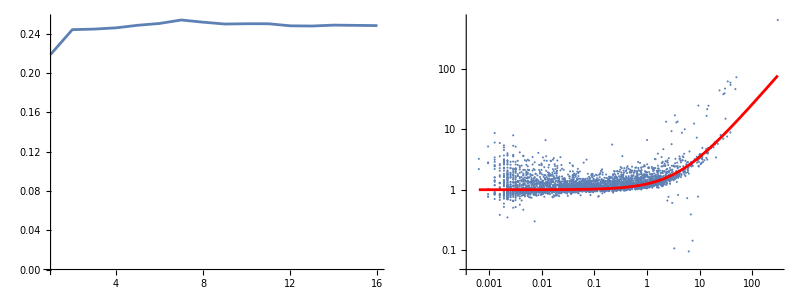

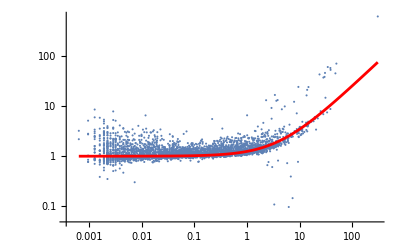

{η→0,θ→0.248263}

```mathematica
rajthetaOnly=TwoComponentCThetaOnly[rajMatpac, "Sample Goal"->5000][[2]]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

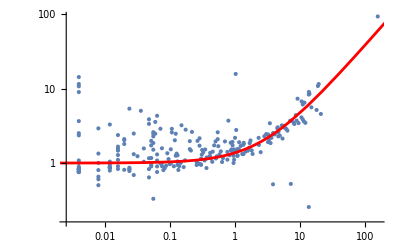

{0.369289}

```mathematica
thetaOnly=Values@TwoComponentCL1AllThetaOnly[smallTestMatpac]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

14683

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

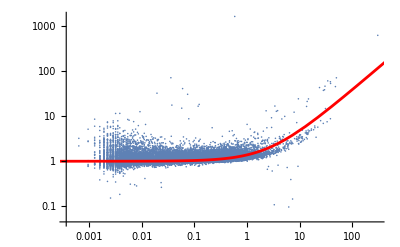

{0.382955}

```mathematica
rajTheta = Values@TwoComponentCL1AllThetaOnly[rajMatpac]
```

```mathematica
Export["thetaOnly.txt", thetaOnly]
```

thetaOnly.txt

```mathematica
Options[BigSurAlt7Test]={"Correlations"-> False, "alpha"-> 0.02, "Pvalue"-> "BH","First Pass Cutoff"-> 2,"Fano Inverse Sqrt Moments"-> True, "Find Communities"-> True};

BigSurAlt7Test[matpac_, η_, θ_,filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{foldername,n,m,z,clist, negccthreshold, mat, depthlist, genetotals, ematrix, pmatrix, mflist,fanocorrectionmatrices, pccmatrix,κlists,ccmats,polylist, polymatrix,equationslist,logplist,pccSignmatrix,augmentedParameters,xlist,equivalentPCCs,logpmatrix, rows,randomematrix,randommat,randompmatrix, randommflist,randomfanocorrectionmatrices,invsqrtmoments,randompolymatrix,randompccmatrix,randomccmats,randompccSignmatrix,randomaugmentedParameters,randomxlist,randomlogpmatrix,cutoff, bhcutoff, bonferroni,sigcutofflevel,sigcutofflist,truesigdata,randomsigdata,significantPCCmatrix,gno, subsetgno,communities,κ1,κ2,κ3,κ4},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
n=Width[mat];
m=Length[genetotals];
clist=√(η/#+ θ)&/@N[genetotals/n];
Print["Started on",CurrentDate[]];
Print["Folder name is"];Print[foldername];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
Share[];
ematrix = KroneckerProduct[genetotals, depthlist];
Share[];
pmatrix =(mat-ematrix)/(√(ematrix(1+clist^2 ematrix)))  ;
Export["residuals.csv", pmatrix];
mflist = 1/(n-1)Total/@(pmatrix^2);
Share[];
Export["mcfanos.csv", mflist];
Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
κ1=FanoCum1[ematrix,clist,n];Share[];
	κ2=FanoCum2[ematrix,clist,n];Share[];
	κ3=FanoCum3[ematrix,clist,n];Share[];
	κ4=FanoCum4[ematrix,clist,n];Share[];
	κlists={κ1,κ2,κ3,κ4};
(*κlists=FanoCumulants5CFAlt[ematrix,clist,n];*);
Export["FK1.csv",κ1];
Export["FK2.csv",κ2];
Export["FK3.csv",κ3];
Export["FK4.csv",κ4];
Share[];
Print["Fano cumulants calculated"];
polylist=CornishFisherPolynomialCoefficientsforFano5CF[κlists[[1]],κlists[[2]],κlists[[3]],κlists[[4]],mflist];
Share[];
Print["Cornish-Fisher coefficients calculated"];
Export["FCF1.csv",polylist[[1]]];
Export["FCF2.csv",polylist[[2]]];
Export["FCF3.csv",polylist[[3]]];
Export["FCF4.csv",polylist[[4]]];
Export["FCF5.csv",polylist[[5]]];
Share[];
pccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
Export["pccmatrix.csv", pccmatrix];
Print["Modified corrected correlations acquired and saved ",TimeObject[Now]];
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
If[OptionValue["Fano Inverse Sqrt Moments"]==True,
invsqrtmoments=InverseSqrtMomentListsAltNew[genetotals,depthlist, η, θ, n];
Export["invsqrtmoments.mx", invsqrtmoments];
Print["inverse squareroot Fano moments acquired and saved ",TimeObject[Now]];
Share[];
fanocorrectionmatrices=SqrtCorrectionmats[invsqrtmoments,genetotals],
fanocorrectionmatrices=Table[ ConstantArray[1,{m,m}],4];
Print["inverse squareroot Fano moments ignored "]];
ccmats=CorrelationCumulantsNewCFAlt[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],fanocorrectionmatrices[[4]],clist,n];
Export["CK1.csv", ccmats[[1]]];
Export["CK2.csv", ccmats[[2]]];
Export["CK3.csv", ccmats[[3]]];
Export["CK4.csv", ccmats[[4]]];
]
```

```mathematica
Directory[]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica

```mathematica
thetaOnly[[1]]
```

0.369289

```mathematica
SetDirectory[".."]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests

```mathematica
SetDirectory["RajThetaOnly"];
```

```mathematica
rajTheta[[1]]
```

0.382955

```mathematica
BigSurAlt7Test[rajMatpac,η/.rajthetaOnly2[[2]],θ/.rajthetaOnly2[[2]],"x", "Correlations"->True ]
```

Started onMon 28 Sep 2026 10:43:04GMT-7

Folder name is

foldername$61240

Modified, corrected Fano factors acquired and saved10:44:54GMT-7TimeObject[{10,44,54.215525},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Modified corrected correlations acquired and saved 10:54:21GMT-7TimeObject[{10,54,21.627435},Instant,-7.]

inverse squareroot Fano moments acquired and saved 10:57:05GMT-7TimeObject[{10,57,5.820942},Instant,-7.]

```mathematica
SetDirectory["OneComponent"];
BigSurAlt7Test[smallTestMatpac, 0., thetaOnly[[1]],"x", "Correlations"->True ]
```

Started onFri 25 Sep 2026 16:20:55GMT-7

Folder name is

foldername$48786

Modified, corrected Fano factors acquired and saved16:20:56GMT-7TimeObject[{16,20,56.327578},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Modified corrected correlations acquired and saved 16:20:58GMT-7TimeObject[{16,20,58.88966},Instant,-7.]

inverse squareroot Fano moments acquired and saved 16:25:13GMT-7TimeObject[{16,25,13.41612},Instant,-7.]

```mathematica
SetDirectory[".."];
(*CreateDirectory["TwoComponent"];*)
SetDirectory["TwoComponent"]
```

/Users/bigcomputer/Desktop/UCI/LanderLab/BigSur/tests/mathematica/TwoComponent

```mathematica
BigSurAlt7Test[smallTestMatpac, etaTheta[[1]], etaTheta[[2]],"x", "Correlations"->True ]
```

Started onFri 25 Sep 2026 15:59:42GMT-7

Folder name is

foldername$38926

Modified, corrected Fano factors acquired and saved15:59:43GMT-7TimeObject[{15,59,43.745868},Instant,-7.]

Fano cumulants calculated

Cornish-Fisher coefficients calculated

Modified corrected correlations acquired and saved 15:59:46GMT-7TimeObject[{15,59,46.308736},Instant,-7.]

inverse squareroot Fano moments acquired and saved 16:04:04GMT-7TimeObject[{16,4,4.054545},Instant,-7.]

```mathematica
Export["test_Genes.csv",smallTestMatpac[[2]]]
```

test_Genes.csv

```mathematica
Context[FanoCum1]
```

Global`

```mathematica
?FanoCum1
```